```mathematica
ExpectedValue[Abs[Exp[#1-1/2t]-1]&,NormalDistribution[0,Sqrt[t]]]
```

2 Erf[(√t)/(2 √2)]

```mathematica
p[t_]:=4(th[Sqrt[t]/2]-1/2)
```

```mathematica
th[x_]:=1/2(1+Erf[x/Sqrt[2]])
```

```mathematica
pl[t1_,t2_]:=Show[

Plot[p[x],{x,0,0.9},AxesLabel->{t,Ε[Abs[Subscript[S, t]-Subscript[S, 0]]]},PlotStyle->Directive[Darker[Darker[Blue]]],Ticks->{{{t1,"t1"},{t2,"t2"}},{}},
Epilog->{Text[Style["long-side arbitrage",FontSize->12],{(Max[t2,t1]+0.9)/2,0.5Min[p[t2],p[t1]]}],
Text[Style["short-side arbitrage",FontSize->12],{(t2+t1)/2,0.5(p[0.9]+Max[p[t2],p[t1]])}]}],

RegionPlot[{y<p[t1],y>p[t2]},{x,0,0.9},{y,0,p[0.9]*1.2},BoundaryStyle->Directive[Opacity[0]],PlotStyle->{Directive[Opacity[0.3],Blue],Directive[Purple,Opacity[0.3]]}],

Graphics[Line[{
{{t1,0},{t1,p[t1]}},
{{t2,0},{t2,p[t2]}}
}]]
];
Manipulate[pl[t1,t2],{{t1,0.23},0,0.9},{{t2,0.4},0,0.9}]
```

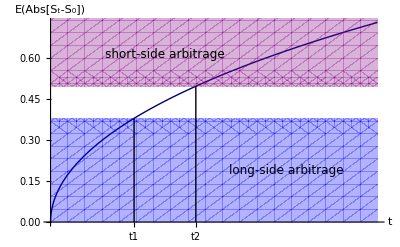

```mathematica
pl[0.23,t2=0.4]
```

```mathematica
Export["c:\\arbband.jpg",pl[0.23,t2=0.4]]
```

c:\arbband.jpg

```mathematica
ExpectedValue[Max[ Exp[#-1/2t]-k,0]&,NormalDistribution[0,Sqrt[t]]]
```

Piecewise[{{1-k, k≤0||t≤0}, {1/2 (1+Erf[(t-2 Log[k])/(2 √2 √t)]-k Erfc[(t+2 Log[k])/(2 √2 √t)]), True}}]

```mathematica
BS[S_,K_,t_]:=S 1/2 (1+Erf[(t-2 Log[k])/(2 √2 √t)]-k Erfc[(t+2 Log[k])/(2 √2 √t)])/.k->K/S
```

```mathematica
P[S_,K_]:=Max[S-K,0];
```

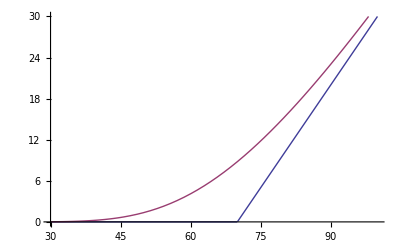

```mathematica
Plot[{P[S,70],BS[S,70,0.1]},{S,30,100},PlotRange->{0,30}]
```